This is the notebook used to create the plot of the Section `Updates’ in the GFE Paper.

```mathematica
(* Update the JDBC driver for Sqlite3 *)
Needs["JLink`"];
Needs["DatabaseLink`"]; (* to import the data from the SQLite3 database *)
ReinstallJava[JVMArguments -> "-Xmx16384m"]; 
AddToClassPath[FileNameJoin[{NotebookDirectory[], "data/sqlite-jdbc-3.32.3.2.jar"}] ,Prepend->True];
Get[FileNameJoin[{NotebookDirectory[], "common.wl"}]]
```

# Import the input data

```mathematica
db = OpenSQLConnection[ JDBC["SQLite", FileNameJoin[{NotebookDirectory[], "data/data21.sqlite3"}] ] ]
```

SQLConnection[…]

```mathematica
allUpdates = sqldataset[ db, "
	SELECT exec_id, client_graph, library, compiler_family, num_threads, outcome, build_frequency_millisecs, num_build_invocations, num_snapshots_created, completion_time_usecs, throughput, driver_release_memory, memfp, memfp_rss, memfp_bytes 
	FROM view_updates 
	WHERE cluster = 'stones2' AND aging = 10 AND NOT is_directed AND omp_threads IS NULL AND NOT has_latency 
"];
```

```mathematica
(* remove the full path from client_graph, convert the attribute into graph *)
allUpdates = allUpdates[ Replace[#, match: KeyValuePattern["client_graph" -> t_String] :> Merge[ {KeyDrop[match, "client_graph"], "graph"-> StringReplace[t, RegularExpression[".*/(.+).properties"] ->  "$1"] }, Last], All] & ];
(* convert driver_release_memory into a boolean *)
allUpdates = allUpdates[Replace[#, match: KeyValuePattern["driver_release_memory" -> t_] :> Merge[ {KeyDrop[match, "driver_release_memory"], "driver_release_memory"-> If[t == 1, True, False]}, Last], All] & ];
(* convert "memfp" into a boolean, rename it in "has_memfp" *)
allUpdates = allUpdates[Replace[#, match: KeyValuePattern["memfp" -> t_] :> Merge[ {KeyDrop[match, "memfp"], "has_memfp"-> If[t == 1, True, False]}, Last], All] & ];
(* rename "memfp_rss" into "rss" and transform into a boolean *)
allUpdates = allUpdates[Replace[#, match: KeyValuePattern["memfp_rss" -> t_] :> Merge[ {KeyDrop[match, "memfp_rss"], "rss"-> If[t == 1, True, False]}, Last], All] & ];
(* convert memory_footprint into gigabytes *)
allUpdates = allUpdates[Replace[#, match: KeyValuePattern["memfp_bytes" -> t_] :> 
Merge[ {KeyDrop[match, "memory_footprint_bytes"], "memory_footprint"-> N[ UnitConvert[ Quantity[If[t === Null, 0, t], "Bytes"], "Gigabytes"] ]}, Last], All] & ];
(* convert the completion time in minutes *)
allUpdates = allUpdates[Replace[#, match: KeyValuePattern["completion_time" -> t_] :> Merge[ {KeyDrop[match, "completion_time"], "completion_time"-> N[UnitConvert[ t, "Minutes"]] }, Last], All] & ];
(* convert the build frequency in seconds *)
allUpdates = allUpdates[Replace[#, match: KeyValuePattern["build_frequency" -> t_] :> Merge[ {KeyDrop[match, "build_frequency"], "build_frequency"-> UnitConvert[ t, "Seconds"] }, Last], All] & ];
(* rename the attributes num_build_invocations, num_snapshots created, driver_release_memory and compiler_family *)
allUpdates = allUpdates[All, KeyMap[Replace[<|"num_snapshots_created" -> "num_deltas", "num_build_invocations"-> "num_builds", "driver_release_memory"  -> "release_memory", "compiler_family" -> "compiler" |>]]];
(* finally reorder the attributes *)
allUpdates = allUpdates[All, {"exec_id", "graph", "library", "compiler", "num_threads", "outcome", "build_frequency", "num_builds", "num_deltas", "completion_time", "throughput", "has_memfp", "release_memory", "rss", "memory_footprint"}]; 
(* updates is the dataset including the results that contain a memory footprint *)
updates = allUpdates[Select[! #"has_memfp" &]]; (* ignore the results that computed the memory footprint *)
(* okay to understand the next filter ;-)
  - has_memfp -> True: it means that the experiment measured for the memory footprint;
    - rss -> True: it means we are measuring the linux RSS (physical memory) of the process. If it were false, it is the 
    "hybrid approach" (see CWI MADAM Jan 2021),  that is the virtual memory for tcmalloc and rss for custom allocators; 
    - release_memory -> False: it implies that the driver does not release the edges that have loaded from the input file 
   and inserted in whatever target library. If the driver were to release the edges (as in the normal executions of the 
 experiment), these chunks of memory could or could not be reused by the target library, due to the multithreaded
   behaviour of tcmalloc. It'd depend on factors like luck and the natural inclination of the sun.
- memory_footprint ≠ 0: the results with memory_footprint == 0 are old executions before the experiment was properly 
   implemented.
- outcome ≠ "timeout": the outcome must be "completed" or "memory_overflow". If it is timeout, we don't have a reading 
     for the whole execution. The outcome `timeout' should be present only in normal executions (without memory footprint) 
     to avoid an experiment taking 1 month to complete. 
*)
updatesMem = allUpdates[Select[#"has_memfp" && ! #"release_memory" && #"rss" && QuantityMagnitude[#"memory_footprint"] ≠ 0 && #"outcome" ≠ "timeout"&]];
```

```mathematica
Dataset[updates, MaxItems-> {10, All}]
```

Dataset[<>]

Just for my own understanding, for which graphs, libraries and parallelism degree we have results?

```mathematica
Dataset[  updates[  GroupBy[<|"library" -> #"library", "compiler" -> #"compiler", "graph" -> #"graph" |>  &] , <| "num_threads" ->  StringRiffle[ Union[ #"num_threads"& /@  #], ", " ]  |> & ][Normal]  [ All, Apply[Join]][SortBy[{#"library", #"compiler", #"graph"} &]], MaxItems->All]
```

Same for the memory footprint:

```mathematica
Dataset[  updatesMem[  GroupBy[<|"library" -> #"library", "compiler" -> #"compiler", "graph" -> #"graph" |>  &] , <| "num_threads" ->  StringRiffle[ Union[ #"num_threads"& /@  #], ", " ]  |> & ][Normal]  [ All, Apply[Join]][SortBy[{#"library", #"compiler", #"graph"} &]], MaxItems->All]
```

Give a canonical name to each platform, before my sanity goes out of window:

```mathematica
(* Previous results, before the camera-ready version, compiled with Clang *)
(*graphone = "g1_v4c-ref-ignore-build"; graphoneMem = "g1_v4-ref-ignore-build";
livegraph = "livegraph_rw"; livegraphMem = "livegraph_rw";
llama = "llama6b-ref"; llamaMem = "llama6-ref";
stinger = "stinger5-ref"; stingerMem = "stinger5-ref";
teseo = "teseo.7"; teseoMem = "teseo.7";*)
(* New results, for the camera ready paper, compiled with GCC *) 
graphone  = "g1_v4-ref-ignore-build"; graphoneMem = graphone;
livegraph = "livegraph_ro"; livegraphMem = livegraph;
llama = "llama6-ref"; llamaMem = llama;
stinger = "stinger5-ref"; stingerMem = stinger;
teseo = "teseo.9"; teseoMem =teseo;
```

For each graph, library and number of threads, show  the median completion time together with its execution ID:

```mathematica
selectMedian[lst_List] := With[ { l = Sort[lst, Order[#1["throughput"] ,#2["throughput"]] &]}, l[[ Ceiling[Length[l] /2 ] ]] ];
medians = Values [   updates[GroupBy[{#"graph", #"library", #"compiler", #"num_threads"} &],  selectMedian] ] [SortBy[{#"library", #"graph", #"compiler", #"num_threads"} & ] ];
mediansMem = Values [   updatesMem[GroupBy[{#"graph", #"library", #"compiler", #"num_threads"} &],  selectMedian] ] [SortBy[{#"library", #"graph", #"compiler", #"num_threads"} & ] ];
```

```mathematica
Dataset[medians, MaxItems-> {10, All}]
```

```mathematica
Dataset[mediansMem, MaxItems-> {10, All}]
```

Collect the list of exec_id, to avoid fetching the throughput of all executions from the database:

```mathematica
lstExecIds= "( " <>StringRiffle[ Normal [ medians[All, "exec_id"] ], ", " ] <> ") "; (* this creates a list such as (7, 42, 248, ...) *)
lstExecIdsMem= "( " <>StringRiffle[ Normal [ mediansMem[All, "exec_id"] ], ", " ] <> ") ";
```

```mathematica
(* the following query is going to take a while to be evaluated by SQLite. ZzZ.... *)
throughputData = sqldataset[db,  "
SELECT exec_id, second, num_operations, throughput 
FROM view_updates_throughput 
WHERE exec_id IN " <> lstExecIds
];
```

Throughput for each library graph, library and parallelism degree:

```mathematica
Options[throughput] = { "Frequency" -> 1, "Compiler" ->  "gcc" };
throughput[library_, graph_, parallelism_, OptionsPattern[]] := Module[ { eid, data},
eid = Normal [ medians[Select[#"graph" ==graph && #"library" == library && #"num_threads" == parallelism && #"compiler" == OptionValue["Compiler"] &], "exec_id" ] ][[1]];
data = throughputData[Select[#"exec_id" == eid &], {"second", "throughput"} ][SortBy["second"] ] // Values // Normal;
Select[ data, Mod[#[[1]], OptionValue["Frequency"]] == 0 & ]
]
```

Memory footprint for the selected executions:

```mathematica
memoryFootprintData = sqldataset[db, "
SELECT exec_id, second, progress, memory_usage_bytes 
FROM view_updates_memory_footprint
WHERE exec_id IN " <> lstExecIdsMem ];
```

```mathematica
Options[memuse] = {"Compiler" -> "gcc"};
memuse[library_, graph_, parallelism_, OptionsPattern[]] := Module[ {eid, data},
eid = Normal [ mediansMem[Select[#"graph" ==graph && #"library" == library && #"num_threads" == parallelism && #"compiler" == OptionValue["Compiler"] &], "exec_id" ] ][[1]];
data = memoryFootprintData[Select[#"exec_id" == eid &], {"progress", "memory_usage_bytes"} ][SortBy["progress"] ] // Values // Normal;
data
]
```

Load the data points once and for all:

```mathematica
G500Stinger = throughput[stinger, "graph500-24", 40];
G500LLAMA = throughput[llama, "graph500-24", 16, "Frequency" -> 10];
(*G500LLAMAWithFreq1 = throughput[llama, "graph500-24", 16];*)
G500GraphOne = throughput[graphone, "graph500-24", 20];
G500LiveGraph = throughput[livegraph, "graph500-24", 20];
G500Teseo = throughput[teseo, "graph500-24", 40];
UnifStinger = throughput[stinger, "uniform-24", 40];
UnifLLAMA = throughput[llama, "uniform-24", 16, "Frequency" -> 10];
UnifGraphOne = throughput[graphone, "uniform-24", 20];
(*UnifGraphOneJuly20 = throughput["g1_v3-ref-ignore-build", "uniform-24", 16]; (* old results presented in the first submission of the paper, July 2020 *)*)
UnifLiveGraph = throughput[livegraph, "uniform-24", 20];
UnifTeseo = throughput[teseo, "uniform-24", 40];
```

```mathematica
With[{graph ="graph500-24"},
MemG500Stinger = memuse[stingerMem, graph, 40];
MemG500LLAMA = memuse[llamaMem, graph, 16];
MemG500GraphOne = memuse[graphoneMem, graph, 20];
MemG500LiveGraph = memuse[livegraphMem, graph, 20];
MemG500T1LiveGraph = memuse["livegraph_rw", graph, 1, "Compiler"-> Null];
MemG500Teseo = memuse[teseoMem, graph, 40];
MemG500T1Teseo = memuse[teseoMem, graph, 1];
];
With[{graph ="uniform-24"},
MemUnifStinger = memuse[stingerMem, graph, 40];
MemUnifLLAMA = memuse[llamaMem, graph, 16];
MemUnifGraphOne = memuse[graphoneMem, graph, 20];
MemUnifLiveGraph = memuse[livegraphMem, graph, 20];
(*MemUnifT1LiveGraph = memuse["livegraph_rw", graph, 1, "Compiler" -> Null];*)
MemUnifTeseo = memuse[teseoMem, graph, 40];
MemUnifT1Teseo = memuse[teseoMem, graph, 1];
];
```

Data for the average throughput

```mathematica
averageThroughput = {
{ (* stinger *)
medians[Select[#"graph" == "graph500-24" && #"library" == stinger && #"num_threads" == 40 &], "throughput"][[1]],
medians[Select[#"graph" == "uniform-24" && #"library" == stinger && #"num_threads" == 40 &], "throughput"][[1]]
},
{ (* llama *)
medians[Select[#"graph" == "graph500-24" && #"library" == llama && #"num_threads" == 16 &], "throughput"][[1]],
medians[Select[#"graph" == "uniform-24" && #"library" == llama && #"num_threads" == 16 &], "throughput"][[1]]
},
{ (* graphone *)
medians[Select[#"graph" == "graph500-24" && #"library" == graphone && #"num_threads" == 20 &], "throughput"][[1]],
medians[Select[#"graph" == "uniform-24" && #"library" == graphone && #"num_threads" == 20 &], "throughput"][[1]]
},
{ (* livegraph *)
medians[Select[#"graph" == "graph500-24" && #"library" == livegraph && #"num_threads" == 20 &], "throughput"][[1]],
medians[Select[#"graph" == "uniform-24" && #"library" == livegraph && #"num_threads" == 20 &], "throughput"][[1]]
},
{ (* teseo *)
medians[Select[#"graph" == "graph500-24" && #"library" == teseo && #"num_threads" == 40 &], "throughput"][[1]],
medians[Select[#"graph" == "uniform-24" && #"library" == teseo && #"num_threads" == 40 &], "throughput"][[1]]
}
};
```

# Plot

```mathematica
pt = 506.0/363; (* mysteriously it scales `points' to its own dimensions *) 
figureWidth := 506pt;
plotHeight := 100pt;
plotStart := 20pt;
ticks = Table[{10^i, Superscript[10, i]}, {i, 1, 5}];
```

```mathematica
colors :=  AssociationThread[{ "Stinger", "LLAMA", "GraphOne", "LiveGraph", "Teseo"}, {Blue,Orange, Darker[Green], Brown, Red}] (* Take[ ColorData[97, "ColorList"], 3] *)
```

```mathematica
marker[symbol_] := Graphics[{Line[{{0,0.5},{4, 0.5}}], Rectangle[{5,-0.5}, {7, 1.5}],  Style[Text[symbol, {2, 0.5}], 14] }]
legend := Row[{
PointLegend[Values[colors],Keys[colors], LegendLayout->{"Row", 1}, LabelStyle->{FontSize-> 8}, LegendMarkers-> marker/@  { "○", "★",  "□", "▽", "◇"}, LegendMarkerSize->25, LegendMargins->0],
Spacer[35],
SwatchLegend[{Black, HatchFilling[]},{"Graph500 SF 24", "Uniform SF 24"}, LegendLayout->{"Row", 1}, LabelStyle->{FontSize-> 8}, LegendMargins->0]
}]
```

```mathematica
legend
```

```mathematica
commonOptions[numSystems_] := {
Frame -> True, 
Joined-> Join[Array[True&, numSystems], Array[False&, numSystems]],
LabelStyle -> {FontSize-> 7},
PlotStyle-> AbsoluteThickness[0.5],
GridLinesStyle -> Directive[AbsoluteDashing[2], AbsoluteThickness[0.5], GrayLevel[.8]],
 AspectRatio-> Full 
};
```

```mathematica
(* Scale the data by 1024, to avoid messing up with the labels in the BarChart *)
averageThroughputScaled = Map [# / 1024 &, averageThroughput, {2}] ;
formatQuantity[value_] := Which [ 
value > 1024, StringForm["`` M", N[NumberForm[value / 1024,{16, 2}]]],
True, StringForm["`` k", N[NumberForm[value,{16, 2}]]]
]
```

#### Plot markers

To show the markers, we sample a bunch of points from the actual data, and add the plot markers  only to those points:

```mathematica
sampledMarkers := With[{markers= {#, 10} &/@ { "○", "★",  "□", "▽", "◇"}},
Join[Array[Spacer[0] & , Length[markers]], markers]
];
sampledMarkers = Append[ Most[sampledMarkers], {"◇",12}];
(*sampledMarkersMem := With[{markers= {#, 10} &/@ { "○", "★",  "□", "▽", "◇", "▽", "◇"}},
Join[Array[Spacer[0] & , Length[markers]], markers]
];*)
```

```mathematica
(* in the updates, sample a point every 10 minutes *)
 sampleUpdates[ lst_ ] := Module[ {next = 300},
DeleteCases[lst, t_List /;If[t[[1]]> next && t[[2]] > 10^4, Module[{}, next = Floor[(t[[1]] + 600) / 600] * 600 ;  False], True], {2}]
]
```

```mathematica
appendMarkersForUpdates[ points_ ] := Join[  points, sampleUpdates /@ points ]
```

```mathematica
(* in the memory usage, select the first point after 0.1, 0.2, 0.3, so on... *)
sampleMemoryUsage[ lst_ ] := Module[ {next = 0.1},
DeleteCases[lst, t_List /;If[t[[1]]> next, Module[{}, next = next + 0.1; False], True], {2}]
]
```

```mathematica
appendMarkersForMemoryUsage[ points_ ] := Join[  points, sampleMemoryUsage /@ points ]
```

#### Frame ticks

```mathematica
minutes = Table[{i * 60, i}, {i, 0, 240, 30}];
```

```mathematica
magnitudes = Table[{10^i, Superscript[10, i]},{i, 0, 9, 1}] ;
```

```mathematica
mergeTicks[ majorTicks_List, minorTicks_List] := Join [ majorTicks,  Select[minorTicks,  Count[ majorTicks, {x_, ___}/; x == #[[1]] ] == 0 & ]] ;
ticksMajorLen := {.02, 0};
ticksMinorLen := {.01, 0};
```

```mathematica
magnitudeTicksMajor =Table[{10^i, If[Mod[i, 2] == 0,Superscript[10, i], Spacer[0]], ticksMajorLen},{i, 0, 9, 1}] ;
magnitudeTicksMinor = Flatten[ Table[{j * 10^i, Spacer[0], ticksMinorLen},{i, 0, 9, 1}, {j, 1, 9, 1}], 1 ];
magnitudeTicks = mergeTicks[magnitudeTicksMajor, magnitudeTicksMinor];
barChartTicksMajor = Table[{10^i/10^3, Superscript[10, i], ticksMajorLen },{i, 0, 9, 1}] ;
barChartTicksMinor = Flatten[ Table[{j * 10^i/10^3, Spacer[0], ticksMinorLen},{i, 0, 9, 1}, {j, 1, 9, 1}], 1 ];
barChartTicks =mergeTicks[ barChartTicksMajor, barChartTicksMinor];
```

```mathematica
memoryTicksMajor = Table[ {i * 32 * 1024^3, i * 32, ticksMajorLen}, {i, 0, 20}];
memoryTicks = memoryTicksMajor;
```

```mathematica
LineLegend[ {{AbsoluteThickness[0.5], Black}, {AbsoluteThickness[0.5], Dotted},  Red},{"p best", "p = 1"}, LabelStyle-> {FontSize-> 7}, LegendMarkerSize-> 10]
```

#### Plot handle

```mathematica
handle = Graphics[ {
Inset[legend, Offset[{0, 0}, ImageScaled[  {0.985, 1} ] ], {Right, Top}],
Inset [  
ListPlot[
{
Style[G500Stinger, colors["Stinger"], AbsoluteThickness[ 0.5], Opacity[0.66]],
Style[G500LLAMA, colors["LLAMA"], Opacity[0.5]],
Style[G500GraphOne, colors["GraphOne"], Opacity[1]],
Style[G500LiveGraph, colors["LiveGraph"], Opacity[0.66]],
Style[G500Teseo, colors["Teseo"], Opacity[0.75]]
} // appendMarkersForUpdates,
FrameLabel-> {{"Throughput [edges/sec]", None}, {"Time [minutes]", None}},
FrameTicks -> {{magnitudeTicks, None}, {minutes, None}},
GridLines->{ #[[1]] &/@ minutes, Table[10^i,{i, 1, 7, 1}]},
ScalingFunctions -> {"Linear", "Log"},
ImageSize-> {1/4 * figureWidth, plotHeight},
PlotLabel-> Style["a) Updates on Graph500-24", Black], 
PlotRange->{  {0, 2 * 60 * 60}, {1, 10^8}},
PlotMarkers-> sampledMarkers,
commonOptions[5]
], Offset[ {0, - plotStart }, Scaled[{0,1}]], {Left, Top}],
Inset [  
ListPlot[
{
Style[UnifStinger, {colors["Stinger"], AbsoluteThickness[ 0.5], Opacity[0.5]}], 
Style[UnifLLAMA, colors["LLAMA"], Opacity[0.5]],
Style[UnifGraphOne, colors["GraphOne"], Opacity[0.5]],
Style[UnifLiveGraph, colors["LiveGraph"], Opacity[0.5]],
Style[UnifTeseo, colors["Teseo"], Opacity[1]]
} // appendMarkersForUpdates,
FrameLabel-> {{"Throughput [edges/sec]", None}, {"Time [minutes]", None}},
FrameTicks -> {{magnitudeTicks, None}, {minutes, None}},
GridLines->{ #[[1]] &/@ minutes, Table[10^i,{i, 1, 7, 1}]},
ScalingFunctions -> {"Linear", "Log"},
ImageSize-> {1/4 * figureWidth, plotHeight},
PlotLabel-> Style["b) Updates on Uniform-24", Black], 
PlotRange->{  {0, 2 * 60 * 60}, {1, 10^8}},
PlotMarkers-> sampledMarkers,
commonOptions[5]
], Offset[ {1/4 * figureWidth, - plotStart }, Scaled[{0,1}]], {Left, Top}],
Inset [  
 BarChart[
averageThroughputScaled,
ChartLabels-> {Placed[Style[#, 5]&/@ Keys[colors], Below], None},
ChartStyle-> { Values[colors], {Opacity[1], HatchFilling[45, 1,3]}},
PlotLabel-> Style["c) Average throughput", Black], 
Frame-> True,
FrameLabel-> {{"Throughput [edges/sec]", None}, {"", None}},
FrameTicks -> {{barChartTicks, None}, {None, None}},
GridLines->{ None, Table[10^i,{i, 2, 8, 1}]} ,
GridLinesStyle -> Directive[AbsoluteDashing[2], AbsoluteThickness[0.5], GrayLevel[.8]],
ScalingFunctions->"Log",
(*PlotRange->{1, 10^8}, *)
PlotRange-> {Automatic, 10^5},
ImagePadding->{{All, All}, {20, 0}},
LabelStyle->7,
BarSpacing->{0, 0.4},
LabelingFunction->( Placed[Rotate[Style[formatQuantity[#],{GrayLevel[0], FontSize-> 5}],0.5 Pi],Above] &),
ImageSize-> {1/4 * figureWidth - 5, plotHeight }, AspectRatio->Full
], Offset[ {2/4 * figureWidth, - plotStart }, Scaled[{0,1}]], {Left, Top}],
Inset [  
ListPlot[
{
Style[MemG500Stinger, colors["Stinger"]],
Style[MemG500LLAMA, colors["LLAMA"]],
Style[MemG500GraphOne, colors["GraphOne"]],
Style[MemG500LiveGraph, colors["LiveGraph"]],
Style[MemG500Teseo, colors["Teseo"]]
(*Style[MemG500T1LiveGraph, colors["LiveGraph"], Dashed],
Style[MemG500T1Teseo, colors["Teseo"], Dashed]*)
} // appendMarkersForMemoryUsage,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
 PlotMarkers-> sampledMarkers,
ScalingFunctions -> {"Linear", "Linear"},
ImageSize-> {1/4 * figureWidth , plotHeight}, AspectRatio->Full,
PlotLabel-> Style["d) Memory usage on Graph500-24", Black], 
(*PlotLegends->Placed[LineLegend[ {{AbsoluteThickness[0.7], Black},  {AbsoluteThickness[0.7], Black,Dashing[0.004]}, Black},{"p best throughput", "p = 1"}, LabelStyle-> {FontSize-> 7}, LegendMarkerSize-> 10, LegendLayout->"Row"], {Center, Top} ],*)
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
commonOptions[5]
], Offset[ {3/4 * figureWidth, - plotStart }, Scaled[{0,1}]], {Left, Top}]
}, ImageSize-> {figureWidth, 120pt}, AspectRatio-> Full, ImagePadding->0, ImageMargins-> 0];
Magnify[handle, 2]
```

-Graphics-

Do not export the plot. It crashes Mathematica.

# Data related to the memory footprint

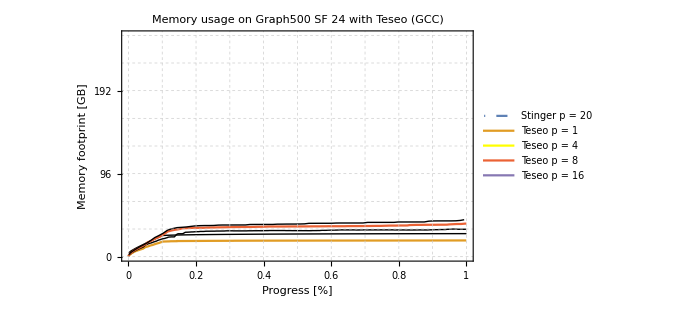
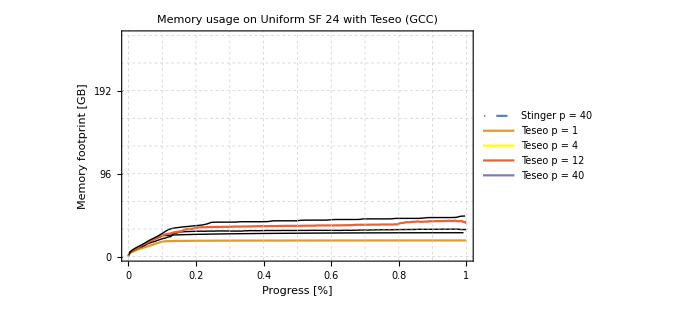

```mathematica
Row [ {ListLinePlot[ {
Style[memuse[stingerMem, "graph500-24", 40], DotDashed],
memuse[teseoMem, "graph500-24", 1],
Style[memuse[teseoMem, "graph500-24", 4], Yellow],
memuse[teseoMem, "graph500-24",12],
Style[memuse[teseoMem, "graph500-24", 40]]
},
PlotLabel->"Memory usage on Graph500 SF 24 with Teseo (GCC)",
Frame-> True,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
GridLinesStyle->Directive[AbsoluteDashing[2],AbsoluteThickness[0.5],GrayLevel[0.8]],
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
PlotLegends->Placed[{"Stinger p = 20", "Teseo p = 1", "Teseo p = 4", "Teseo p = 8", "Teseo p = 16", "Teseo p = 40"}, {Right, Top}],
ImageSize-> 500],
ListLinePlot[ {
Style[memuse[stingerMem, "uniform-24", 40], DotDashed],
memuse[teseoMem, "uniform-24", 1],
Style[memuse[teseoMem, "uniform-24", 4], Yellow],
memuse[teseoMem, "uniform-24", 12],
Style[memuse[teseoMem, "uniform-24", 40]]
},
PlotLabel->"Memory usage on Uniform SF 24 with Teseo (GCC)",
Frame-> True,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
GridLinesStyle->Directive[AbsoluteDashing[2],AbsoluteThickness[0.5],GrayLevel[0.8]],
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
PlotLegends->Placed[{"Stinger p = 40", "Teseo p = 1", "Teseo p = 4", "Teseo p = 12", "Teseo p = 40"}, {Right, Top}],
ImageSize-> 500]
}]
```

How much memory usage consume Teseo with p = 40 w.r.t. Stinger [ p = 40 ] ? First result is graph500-24, second result is uniform-24.

```mathematica
{ N [ memuse[teseoMem, "graph500-24", 40][[-1, 2]] / memuse[stingerMem, "graph500-24", 40][[-1, 2]] ], N [ memuse[teseoMem, "uniform-24", 40][[-1, 2]] / memuse[stingerMem, "uniform-24", 40][[-1, 2]] ] }
```

{1.60391,1.69784}

These are the previous results with Clang. The code should be updated to re-create the plots.

```mathematica
(*grMem = Graphics [{
Inset[legend, Offset[{0, 0}, ImageScaled[  {0.985, 1} ] ], {Right, Top}],
Inset [  
ListPlot[
{
Style[MemG500Stinger, colors["Stinger"]],
Style[MemG500LLAMA, colors["LLAMA"]],
Style[MemG500GraphOne, colors["GraphOne"]],
Style[MemG500LiveGraph, colors["LiveGraph"]],
Style[MemG500Teseo, colors["Teseo"]]
} // appendMarkersForMemoryUsage,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
 PlotMarkers-> sampledMarkers,
ScalingFunctions -> {"Linear", "Linear"},
ImageSize-> {1/2 * figureWidth , 200}, AspectRatio->Full,
PlotLabel-> "d) Memory usage on Graph500-24", 
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
commonOptions[5]
], Offset[ {0, - plotStart }, Scaled[{0,1}]], {Left, Top}],
Inset [  
ListPlot[
{
Style[MemUnifStinger, colors["Stinger"], AbsoluteThickness[1]],
Style[MemUnifLLAMA, colors["LLAMA"]],
Style[MemUnifGraphOne, colors["GraphOne"]],
Style[MemUnifLiveGraph, colors["LiveGraph"]],
Style[MemUnifTeseo, colors["Teseo"]]
} // appendMarkersForMemoryUsage,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
 PlotMarkers-> sampledMarkers,
ScalingFunctions -> {"Linear", "Linear"},
ImageSize-> {1/2 * figureWidth , 200}, AspectRatio->Full,
PlotLabel-> "d) Memory usage on Uniform-24", 
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
commonOptions[5]
], Offset[ {1/2 * figureWidth, - plotStart }, Scaled[{0,1}]], {Left, Top}]
}, ImageSize-> {figureWidth, 170pt}, AspectRatio-> Full, ImagePadding->0, ImageMargins-> 0]; Magnify[grMem,2]*)
```

-Graphics-

Helper function, sample the memory usage after 10%, 20%, 30%, so on..

```mathematica
(*sampleMem[ lst_ ] := Module[ {next = 0.1,  points},
points = Select[lst, With[{t = #}, If[t [[1]]> next, Module[{}, next = next + 0.1; True], False ]]&] ;
If[Last[lst][[1]] > 0.99, AppendTo[points, {1, Last[lst][[2]]}]];
#[[2]] &/@ points
]*)
```

Memory usage difference with Teseo. Apparently we consume 15% more memory with Graph500 than with Uniform-24

```mathematica
(*N[ sampleMem [ MemG500Teseo ] / sampleMem [ MemUnifTeseo ] ]*)
```

{0.909605,0.873768,0.853155,0.84368,0.847046,0.84122,0.852052,0.842511,0.849133,0.850045}

LiveGraph is very consistent in this. Same memory usage with G500 and Uniform

```mathematica
(*N[ sampleMem [ MemG500LiveGraph ] / sampleMem [ MemUnifLiveGraph ] ]*)
```

{0.943259,1.01698,1.03144,1.04257,1.02335,1.03846,1.0543,1.0415,1.0756,1.11107}

In GraphOne, for whatever reason, it consumes less memory with the Uniform graph, still in the range of 5% - 10% though:

```mathematica
(*N[ sampleMem [ MemG500GraphOne ] / sampleMem [ MemUnifGraphOne ] ]*)
```

```mathematica
(*N[ sampleMem [ MemG500Stinger ] / sampleMem [ MemUnifStinger ] ]*)
```

{0.999366,0.983246,0.974186,0.968189,0.964372,0.961713,0.960119,0.959448,0.959563,0.960575}

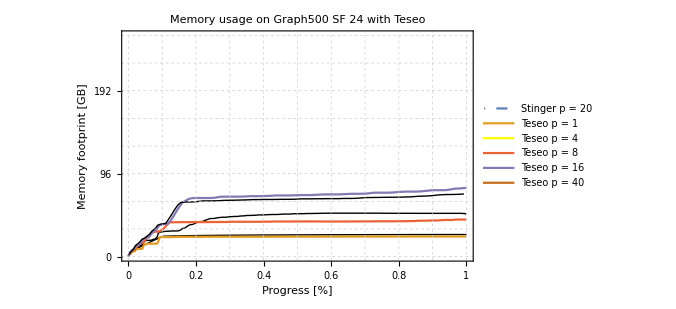
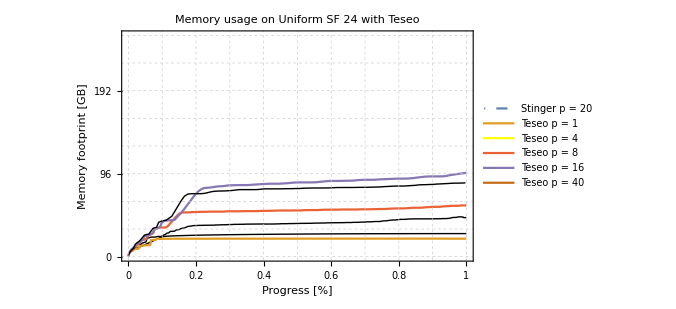

```mathematica
(*Row [ {ListLinePlot[ {
Style[memuse[stingerMem, "graph500-24", 20], DotDashed],
memuse[teseoMem, "graph500-24", 1],
Style[memuse[teseoMem, "graph500-24", 4], Yellow],
memuse[teseoMem, "graph500-24", 8],
memuse[teseoMem, "graph500-24", 16],
Style[memuse[teseoMem, "graph500-24", 40]]
},
PlotLabel->"Memory usage on Graph500 SF 24 with Teseo",
Frame-> True,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
GridLinesStyle->Directive[AbsoluteDashing[2],AbsoluteThickness[0.5],GrayLevel[0.8]],
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
PlotLegends->Placed[{"Stinger p = 20", "Teseo p = 1", "Teseo p = 4", "Teseo p = 8", "Teseo p = 16", "Teseo p = 40"}, {Right, Top}],
ImageSize-> 500],
ListLinePlot[ {
Style[memuse[stingerMem, "uniform-24", 20], DotDashed],
memuse[teseoMem, "uniform-24", 1],
Style[memuse[teseoMem, "uniform-24", 4], Yellow],
memuse[teseoMem, "uniform-24", 8],
memuse[teseoMem, "uniform-24", 16],
Style[memuse[teseoMem, "uniform-24", 40]]
},
PlotLabel->"Memory usage on Uniform SF 24 with Teseo",
Frame-> True,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
GridLinesStyle->Directive[AbsoluteDashing[2],AbsoluteThickness[0.5],GrayLevel[0.8]],
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
PlotLegends->Placed[{"Stinger p = 20", "Teseo p = 1", "Teseo p = 4", "Teseo p = 8", "Teseo p = 16", "Teseo p = 40"}, {Right, Top}],
ImageSize-> 500]
}]*)
```

## Memory footprint (invalid results: RSS + memory released in the driver)

These are the results with an early implementation of the experiment where the memory from the driver was released while the execution was running. The net result is that in all cases, incl. Stinger, the memory footprint increases with time because the memory deallocated from the driver is not released back to the O.S.

```mathematica
(*grMem = Graphics [{
Inset[legend, Offset[{0, 0}, ImageScaled[  {0.985, 1} ] ], {Right, Top}],
Inset [  
ListPlot[
{
Style[MemG500Stinger, colors["Stinger"]],
Style[MemG500LLAMA, colors["LLAMA"]],
Style[MemG500GraphOne, colors["GraphOne"]],
Style[MemG500LiveGraph, colors["LiveGraph"]],
Style[MemG500Teseo, colors["Teseo"]]
} // appendMarkersForMemoryUsage,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
 PlotMarkers-> sampledMarkers,
ScalingFunctions -> {"Linear", "Linear"},
ImageSize-> {1/2 * figureWidth , plotHeight}, AspectRatio->Full,
PlotLabel-> "d) Memory usage on Graph500-24", 
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
commonOptions
], Offset[ {0, - plotStart }, Scaled[{0,1}]], {Left, Top}],
Inset [  
ListPlot[
{
Style[MemUnifStinger, colors["Stinger"], AbsoluteThickness[1]],
Style[MemUnifLLAMA, colors["LLAMA"]],
Style[MemUnifGraphOne, colors["GraphOne"]],
Style[MemUnifLiveGraph, colors["LiveGraph"]],
Style[MemUnifTeseo, colors["Teseo"]]
} // appendMarkersForMemoryUsage,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
 PlotMarkers-> sampledMarkers,
ScalingFunctions -> {"Linear", "Linear"},
ImageSize-> {1/2 * figureWidth , plotHeight}, AspectRatio->Full,
PlotLabel-> "d) Memory usage on Uniform-24", 
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
commonOptions
], Offset[ {1/2 * figureWidth, - plotStart }, Scaled[{0,1}]], {Left, Top}]
}, ImageSize-> {figureWidth, 120pt}, AspectRatio-> Full, ImagePadding->0, ImageMargins-> 0]; Magnify[grMem,2]*)
```

-Graphics-

Memory footprint of the CSR, on the graphs with S.F. 24:

```mathematica
(*MemoryFootprintCSR = UnitConvert[ Quantity[(* num vertices *) 8870942 * (* num edges *) 4 + 260379520 * 8 + (* weights (double) *) 260379520 * 8, "Bytes"], "Gigabytes"] // N*)
```

4.20156 GB

Helper function, sample the memory usage after 10%, 20%, 30%, so on..

```mathematica
(*sampleMem[ lst_ ] := Module[ {next = 0.1,  points},
points = Select[lst, With[{t = #}, If[t [[1]]> next, Module[{}, next = next + 0.1; True], False ]]&] ;
If[Last[lst][[1]] > 0.99, AppendTo[points, {1, Last[lst][[2]]}]];
#[[2]] &/@ points
]*)
```

Memory usage difference with Teseo. Apparently we consume 15% more memory with Graph500 than with Uniform-24

```mathematica
(*N[ sampleMem [ MemG500Teseo ] / sampleMem [ MemUnifTeseo ] ]*)
```

{0.922269,0.937667,1.1751,1.16617,1.17941,1.16187,1.18377,1.16656,1.153,1.16486}

LiveGraph is very consistent in this. Same memory usage with G500 and Uniform

```mathematica
(*N[ sampleMem [ MemG500LiveGraph ] / sampleMem [ MemUnifLiveGraph ] ]*)
```

{0.9614,1.00315,0.944985,0.993767,0.976376,0.986653,1.01359,1.04117,1.02697,1.02248}

In GraphOne, for whatever reason, it consumes less memory with the Uniform graph, still in the range of 5% - 10% though:

```mathematica
(*N[ sampleMem [ MemG500GraphOne ] / sampleMem [ MemUnifGraphOne ] ]*)
```

{0.960415,0.872974,0.934412,0.933998,0.944117,0.949242,0.947439,0.946062,0.951653,0.940514}

Stinger is also very consistent in this:

```mathematica
(*N[ sampleMem [ MemG500Stinger ] / sampleMem [ MemUnifStinger ] ]*)
```

{1.00055,0.988091,0.984289,0.983085,0.982803,0.980166,0.972885,0.977424,0.976837,0.989883}

Comparison with the CSR:

```mathematica
(*Quantity[ Last[MemG500Teseo][[2]] , "Bytes"] / MemoryFootprintCSR*)
```

42.3492

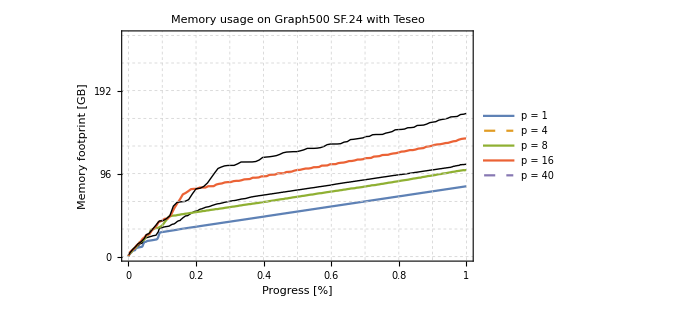
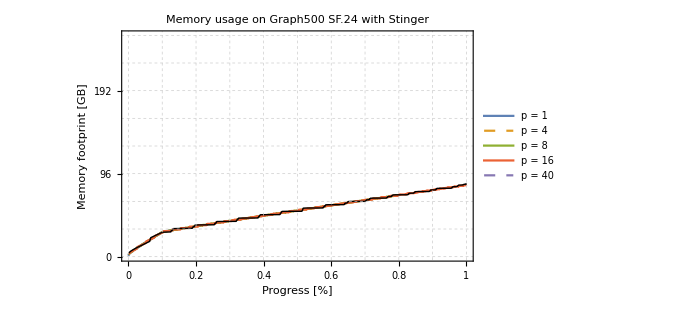

```mathematica
(*Row[ { 
ListLinePlot[ {
memuse[teseo, "graph500-24", 1],
Style[memuse[teseo, "graph500-24", 4], Dashed],
memuse[teseo, "graph500-24", 8],
memuse[teseo, "graph500-24", 16],
Style[memuse[teseo, "graph500-24", 40], Dashed]
},
PlotLabel->"Memory usage on Graph500 SF.24 with Teseo",
Frame-> True,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
GridLinesStyle->Directive[AbsoluteDashing[2],AbsoluteThickness[0.5],GrayLevel[0.8]],
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
PlotLegends->Placed[{"p = 1", "p = 4", "p = 8", "p = 16", "p = 40"}, {Right, Top}],
ImageSize-> 500],
ListLinePlot[ {
memuse[stinger, "graph500-24", 1],
Style[memuse[stinger, "graph500-24", 4], Dashed],
memuse[stinger, "graph500-24", 8],
memuse[stinger, "graph500-24", 16],
Style[memuse[stinger, "graph500-24", 40], Dashed]
},
PlotLabel->"Memory usage on Graph500 SF.24 with Stinger",
Frame-> True,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
GridLinesStyle->Directive[AbsoluteDashing[2],AbsoluteThickness[0.5],GrayLevel[0.8]],
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
PlotLegends->Placed[{"p = 1", "p = 4", "p = 8", "p = 16", "p = 40"}, {Right, Top}],
ImageSize-> 500
]}]*)
```

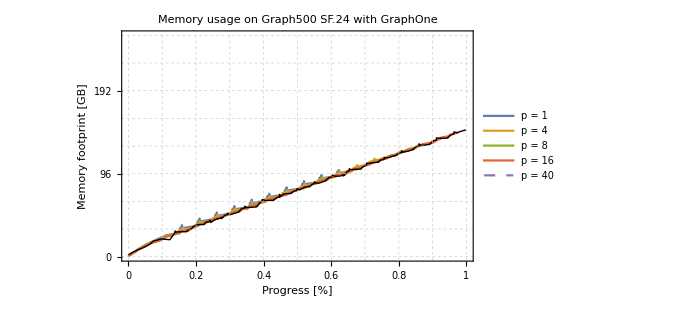
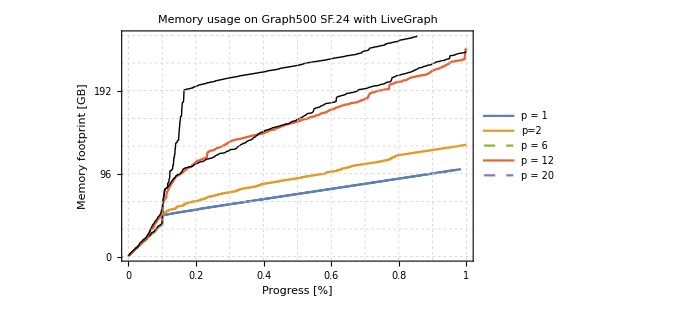

```mathematica
(*Row[ { 
ListLinePlot[ {
memuse[graphone, "graph500-24", 1],
memuse[graphone, "graph500-24", 4],
memuse[graphone, "graph500-24", 8],
memuse[graphone, "graph500-24", 16],
Style[memuse[graphone, "graph500-24", 40], Dashed]
},
PlotLabel->"Memory usage on Graph500 SF.24 with GraphOne",
Frame-> True,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
GridLinesStyle->Directive[AbsoluteDashing[2],AbsoluteThickness[0.5],GrayLevel[0.8]],
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
PlotLegends->Placed[{"p = 1", "p = 4", "p = 8", "p = 16", "p = 40"}, {Right, Top}],
ImageSize-> 500],
ListLinePlot[ {
memuse[livegraph, "graph500-24", 1],
memuse[livegraph, "graph500-24", 2], (* we don't have results with p = 4 *)
Style[memuse[livegraph, "graph500-24", 6], Dashed], (* we don't have results with p = 8 *)
memuse[livegraph, "graph500-24", 12],
Style[memuse[livegraph, "graph500-24", 20], Dashed]
},
PlotLabel->"Memory usage on Graph500 SF.24 with LiveGraph",
Frame-> True,
FrameLabel-> {{"Memory footprint [GB]", None}, {"Progress [%]", None}},
FrameTicks -> {{memoryTicks, None}, {Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], None}},
GridLines->{ Union[{0, 1}, Table[i, {i, 0.1, 0.9, 0.1}]], First /@memoryTicks },
GridLinesStyle->Directive[AbsoluteDashing[2],AbsoluteThickness[0.5],GrayLevel[0.8]],
PlotRange->{  {0, 1}, {0, 256 * 1024^3}},
PlotLegends->Placed[{"p = 1", "p=2", "p = 6", "p = 12", "p = 20"}, {Right, Top}],
ImageSize-> 500]
}

]*)
```